## Chapter 6 Problem 13: Resonance in a partial wave

#### This notebook reproduces Figure 6.15, and also draws the analogy of Figure 6.14

```mathematica
Remove["Global`*"]
```

Set up the problem. Note that we are using the l=3 partial wave. Let x be a scaled version of k.

```mathematica
l=3;
depth=5.5^2;
$Assumptions={R>0,ℏ>0,m>0};
subs={k->x/R,V0->depth ℏ^2/(2m R^2)};
```

Find the wavenumber inside the well and then Al(r), the wave function inside the well, which is simply the spherical Bessel function for a free particle with the right wavenumber.

```mathematica
energy=ℏ^2k^2/(2m);
κ=Sqrt[2m(energy+V0)/ℏ^2];
Al=SphericalBesselJ[l,z];
```

Now calculate the logarithmic derivative (6.139) and use it to find the phase shift (6.140). Use the two-argument form of ArcTan to avoid ambiguity.

```mathematica
βl=(z D[Al,z]/Al)/.z->κ R;
tdlN=x D[SphericalBesselJ[l,x],x]-βl SphericalBesselJ[l,x];
tdlD=x D[SphericalBesselY[l,x],x]-βl SphericalBesselY[l,x];
δl=Simplify[ArcTan[tdlD,tdlN]/.subs];
```

Determine the value of k when the phase shift passes through 90 degrees

```mathematica
xRes=x/.FindRoot[δl==Pi/2,{x,1.4}]
```

1.41114

Plot the cross section for this partial wave from (6.127) as a function of x=kR. Include a plot of the unitarity limit 4π(2l+1)/k^2. This is the top half of Figure 6.15.

```mathematica
σLim=4 Pi (2l+1)/x^2
```

(28 π)/x^2

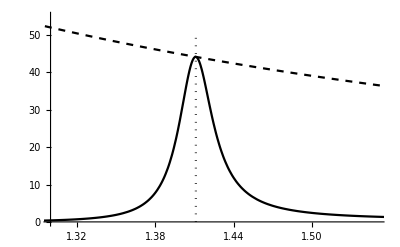

```mathematica
σTot=σLim Sin[δl]^2;
Show[
Plot[{σTot,σLim},{x,1.2,1.8},
PlotStyle->{{Black},{Black,Dashed}},
PlotRange->{{1.3,1.55},{0,55}}],
ListLinePlot[{{xRes,0},{xRes,50}},PlotStyle->{Black,Dotted}]
]
```

Now plot the phase shift as a function of x=kR.  This is the bottom part of the figure.

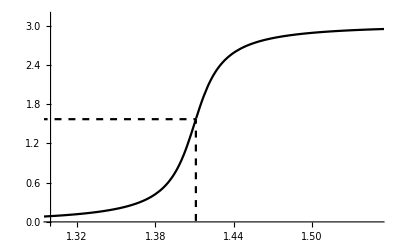

```mathematica
Show[
Plot[δl,{x,1.2,1.8},PlotStyle->Black,
PlotRange->{{1.3,1.55},{0,Pi}}],
ListLinePlot[{{0,Pi/2},{xRes,Pi/2},{xRes,0}},PlotStyle->{Black,Dashed}]
]
```

It is instructive to make a plot of the energy level, the potential well, and the effective potential. Remember that energy is scaled by ℏ^2/2mR^2. (This is the analog of Figure 6.14.)

```mathematica
rMax=4;
eRes=x^2/.x->xRes;
barrier=l(l+1)/r^2;
vEff=depth (HeavisideTheta[r-1]-1)+barrier;
```

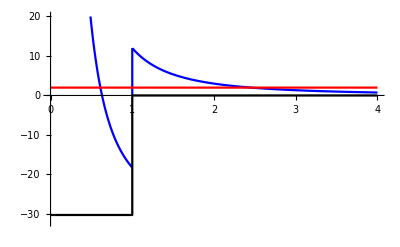

```mathematica
Show[
Plot[vEff,{r,0,4},PlotRange->{-32,20},PlotRange->{-32,20},PlotStyle->Blue],
ListLinePlot[{{1,barrier/.r->1-depth},{1,barrier/.r->1}},PlotStyle->Blue],
ListLinePlot[{{0,eRes},{rMax,eRes}},PlotStyle->Red],
ListLinePlot[{{0,-depth},{1,-depth},{1,0},{rMax,0}},PlotStyle->Black]
]
```